```mathematica
Integrate[Exp[1 - A Cos[θ] - B Sin[θ] +C],θ]
```

∫ⅇ^(1+C-A Cos[θ]-B Sin[θ])ⅆθ

```mathematica
ClearAll[A,B,Const]
Integrate[Exp[1 - A Cos[θ] - B Sin[θ-ϕ] +Const],{θ,0,2π}]
```

∫_0^(2 π) ⅇ^(1+Const-A Cos[θ]-B Sin[θ-ϕ])ⅆθ

```mathematica
ClearAll[A,B,Const,Donst]
Integrate[Exp[1 - A Cos[θ] - B Sin[θ] +Const Cos[θ]^2 ],{θ,0,2π}]
```

∫_0^(2 π) ⅇ^(1-A Cos[θ]+Const Cos[θ]^2-B Sin[θ])ⅆθ

```mathematica
Integrate[Exp[1 - A Cos[θ] - B Sin[θ] +Const],{θ,0,2π}]
```

ConditionalExpression[2 ⅇ^(1+Const) π BesselI[0,√(A^2+B^2)], A∈ℝ&&B∈ℝ]

```mathematica
Integrate[Exp[((A- Cos[θ] )^2+ (B- Sin[θ])^2 )/C],{θ,0,2π}]
```

$Aborted

```mathematica
Integrate[Exp[ A Cos[θ] + B Sin[θ] +Const],{θ,0,2π}]
```

2 ⅇ^Const π Hypergeometric0F1Regularized[1,25/2]

```mathematica
Integrate[Exp[ 10 Cos[θ] + 20 Sin[θ] +1],{θ,0,2π}]
```

2 ⅇ π Hypergeometric0F1Regularized[1,125]

```mathematica
A = -5; B=2; Const= -3;
NIntegrate[Exp[ A Cos[θ] +B Sin[θ] +Const],{θ,0,2π}]
N[2 π Exp[Const] BesselI[0,√(A^2+B^2)]]
```

12.0406

12.0406

```mathematica
σ = 0.2;
x1=1;
x2=0;
xD2 = 0;
NIntegrate[Exp[-((Sin[θ] - x2)^2+(Cos[θ]-x1)^2 + xD2)/(2σ^2) ],{θ,0,2π}]
N[2π Exp[-(1+x1^2+x2^2+xD2)/(2σ^2)]BesselI[0,√((x1^2+x2^2)/σ^4)]]
```

0.503891

0.503891

```mathematica
N[2 π Exp[-10] BesselI[0,√(5^2+5^2)],20]
```

0.051363552186599782073

```mathematica
f[A_]:=2 ⅇ^(1+C) π BesselI[0,√(A^2+B^2)]
FullSimplify[Derivative[f[A],A]]
```

Derivative[2 ⅇ^(1+C) π BesselI[0,√(A^2+B^2)],A]

```mathematica
BesselI[0,0]
```

1

```mathematica
FullSimplify[Derivative[BesselI[0,x],x]]
```

Derivative[BesselI[0,x],x]

```mathematica
Derivative[BesselI[0,x],x]/. x->0.5
```

Derivative[1.06348,0.5]

```mathematica
D[BesselI[0,x],x]/. x->2.5
```

2.51672

```mathematica
BesselI[1,x]/.x->2.5
```

2.51672

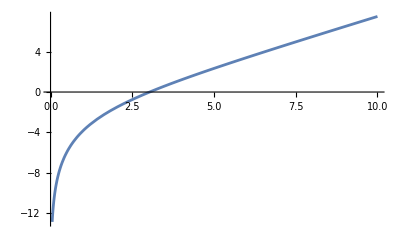

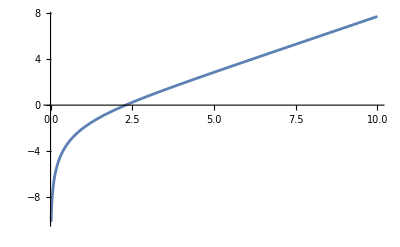

```mathematica
Plot[Log[BesselI[3,x]],{x,0,10}]
Plot[Log[BesselI[2,x]],{x,0,10}]
```

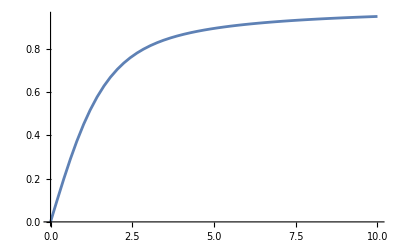

```mathematica
Plot[BesselI[-1,x]/BesselI[0,x],{x,0,10}]
```

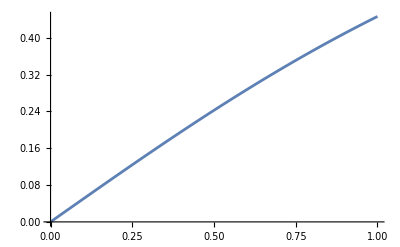

```mathematica
Plot[BesselI[1,x]/BesselI[0,x],{x,0,1}]
```

```mathematica
Plot[x(1-BesselI[2,x]/BesselI[0,x])/2,{x,0,1}]
```

-Graphics-

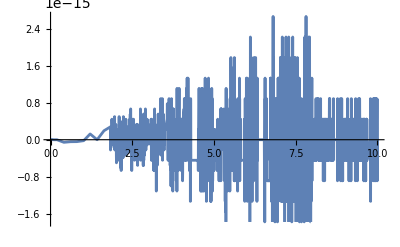

```mathematica
Plot[BesselI[1,x]/BesselI[0,x]-x/2+x BesselI[2,x]/(2 BesselI[0,x]),{x,0,10}]
```

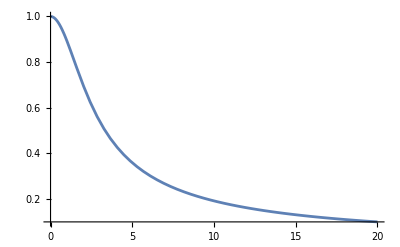

```mathematica
Plot[1 - BesselI[2,x]/( BesselI[0,x]),{x,0,20}]
```

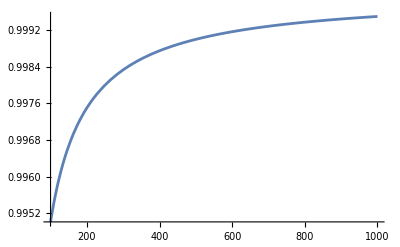

```mathematica
Plot[Exp[-ArcSinh[1/x]+Sqrt[x^2+1]-x],{x,100,1000}]
```

0.9

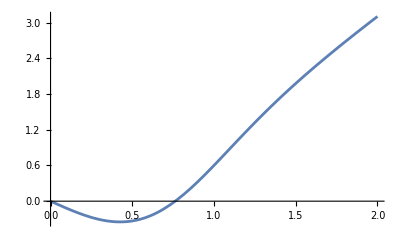

```mathematica
σ=.9
Plot[-(x/σ^2)+(2x/σ^4) BesselI[1,x^2/σ^4]/BesselI[0,x^2/σ^4],{x,0,2}]
```

### Plot of density along x1 axis

0.05

General::munfl: Exp[-999.935] is too small to represent as a normalized machine number; precision may be lost.

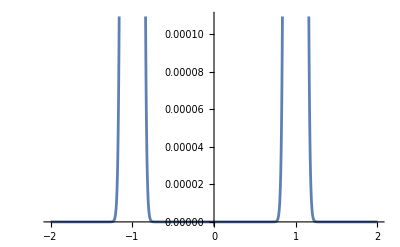

```mathematica
σ=.05
Plot[Exp[-(1+x^2)/(2σ^2)]BesselI[0,x/σ^2],{x,-2,2}]
```

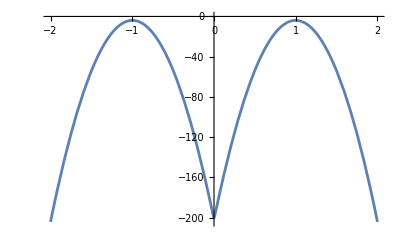

```mathematica
Plot[-(1+x^2)/(2σ^2)+Log[BesselI[0,x/σ^2]],{x,-2,2}]
```

### Plot of score along x1 axis

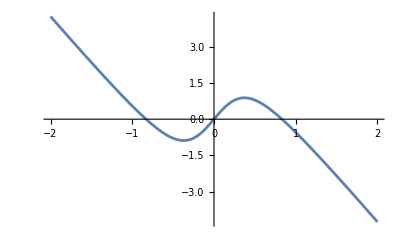

```mathematica
σ=.5;
Plot[-(x)/(σ^2)+1/σ^2 BesselI[1,x/σ^2]/BesselI[0,x/σ^2],{x,-2,2}]
```

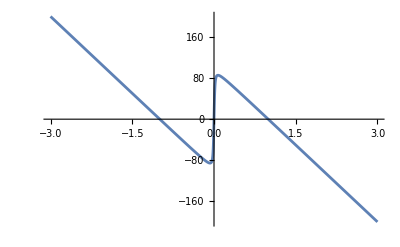

```mathematica
σ=.1;
Plot[-x/σ^2+1/σ^2*BesselI[1,x/σ^2]/BesselI[0,x/σ^2],{x,-3,3}]
```

```mathematica
Plot[Log[BesselI[0,x/σ]]]
```

```mathematica
BesselI[1,0.5]/BesselI[0,0.5]
```

0.2425

```mathematica
ClearAll[x1,x2,σ];
D[√((x1^2+x2^2)/σ^4),x1]
```

x1/(√((x1^2+x2^2)/σ^4) σ^4)

```mathematica
f[s_]:=1/√(1+s^2)
```

```mathematica
D[f[s],s]
```

-s/((1+s^2)^(3/2))

```mathematica
Integrate[(1-L)/(1+s^2)/(L+s^2)s,{s,s1,s2},Assumptions->L>0]
```

ConditionalExpression[1/2 (-Log[-L-s1^2]+Log[1+s1^2]+Log[-L-s2^2]-Log[1+s2^2]), ]

```mathematica
Integrate[Log[x],{x,0,1}]
```

-1

```mathematica
Integrate[k x^(k-1) Log[k x^(k-1)],{x,0,1}]
```

ConditionalExpression[(1-k+k Log[k])/k, Re[k]>0]

```mathematica
Series[Cos[x],{x,a,3}]
```

Cos[a]-Sin[a] (x-a)-1/2 Cos[a] (x-a)^2+1/6 Sin[a] (x-a)^3+O[x-a]^4

```mathematica
ClearAll[G,σ,ψ,θ]
Integrate[Cos[θ]Exp[G (Cos[θ] Cos[ψ]+Sin[θ] Sin[ψ])/σ^2],{θ,-2π,2π}]
```

4 π BesselI[1,G/σ^2] Cos[ψ]

```mathematica
Integrate[Cos[θ]Exp[G (Cos[θ] Cos[ψ]+Sin[θ] Sin[ψ])/σ^2],{θ,-2π,2π}]
Integrate[Sin[θ]Exp[G (Cos[θ] Cos[ψ]+Sin[θ] Sin[ψ])/σ^2],{θ,-2π,2π}]
Integrate[Exp[G (Cos[θ] Cos[ψ]+Sin[θ] Sin[ψ])/σ^2],{θ,-2π,2π}]
```

4 π BesselI[1,G/σ^2] Cos[ψ]

4 π BesselI[1,G/σ^2] Sin[ψ]

4 π BesselI[0,G/σ^2]

```mathematica
ClearAll[ψ,θ]
TrigExpand[ Cos[θ-ψ]]
```

Cos[θ] Cos[ψ]+Sin[θ] Sin[ψ]

```mathematica
N[BesselI[1,5]/BesselI[0,5]]
```

0.893383

```mathematica
FullSimplify[D[(x1 - R1 Cos[x])^2+(x2-R2 Sin[x])^2,{x,2}]]
```

2 (R1 x1 Cos[x]+(-R1^2+R2^2) Cos[2 x]+R2 x2 Sin[x])

```mathematica
R1=3; R2 =1;
x1=25; x2=0;
D[(x1 - R1 Cos[x])^2+(x2-R2 Sin[x])^2,{x,2}]/.x->ArgMin[(x1 - R1 Cos[x])^2+(x2-R2 Sin[x])^2,x]
x1=0; x2=25;
D[(x1 - R1 Cos[x])^2+(x2-R2 Sin[x])^2,{x,2}]/.x->ArgMin[(x1 - R1 Cos[x])^2+(x2-R2 Sin[x])^2,x]
```

134

66

```mathematica
RR = 10;
Plot[D[(RR Cos[θ] - R1 Cos[x])^2+(RR Sin[θ] -R2 Sin[x])^2,{x,2}]/.
x->ArgMin[(RR Cos[θ] - R1 Cos[x])^2+(RR Sin[θ]-R2 Sin[x])^2,x],
{θ,0,2π}]
```

$Aborted

{11.0712,19.2504,27.1084,34.8238,42.1321,48.5741,53.6403,56.8834,58.,56.8834,53.6403,48.5741,42.1321,34.8238,27.1084,19.2504,11.0712,2.}

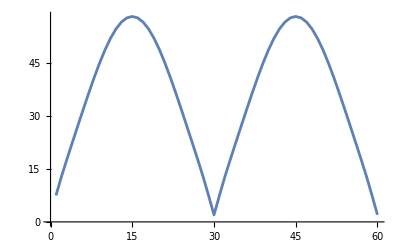

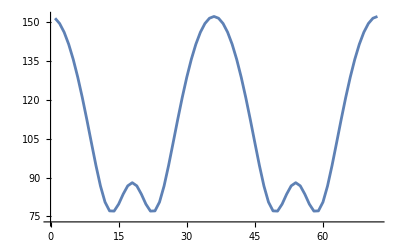

```mathematica
R1=5; R2 =1;
RR = 5;
g[θ_]:=D[(RR Cos[θ] - R1 Cos[x])^2+(RR Sin[θ] -R2 Sin[x])^2,{x,2}]/.
x->ArgMin[(RR Cos[θ] - R1 Cos[x])^2+(RR Sin[θ]-R2 Sin[x])^2,x]
Ngrid = 30;
N[Map[g,Range[18]π/18]]
ListLinePlot[N[Map[g,Range[Ngrid * 2]π/Ngrid]]]
```

```mathematica
N[Map[g,Range[18]π/18]]
```

{43.3827,41.6176,38.9888,36.0441,33.6507,32.7753,33.665,35.2486,36.,35.2486,33.665,32.7753,33.6507,36.0441,38.9888,41.6176,43.3827,44.}

```mathematica
D[1/(1+x^2)^(1/2),{x,1}]
```

-x/((1+x^2)^(3/2))